# Circle Map

### Author

Eric W. Weisstein
September 28, 2003

This notebook downloaded from http://mathworld.wolfram.com/notebooks/DynamicalSystems/CircleMap.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/CircleMap.html.

©2005 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
CircleMap[{K_,Ω_},n_,t0_]:=NestList[Mod[#+Ω-K/(2Pi)Sin[2Pi #],1]&,t0,n]
```

## Plot

```mathematica
<<Graphics`Colors`
Needs["Typesetting`"]
```

Needs::nocont: Context Typesetting` was not created when Needs was evaluated.

```mathematica
color={Red,Yellow,Green,Blue,Violet};
```

```mathematica
MakeBoxes[label[k_,o_],TraditionalForm]:=RowBox[{RowBox[{"K","==",MakeBoxes[k,TraditionalForm]}],",",RowBox[{"Ω","==",MakeBoxes[o,TraditionalForm]}]}]
```

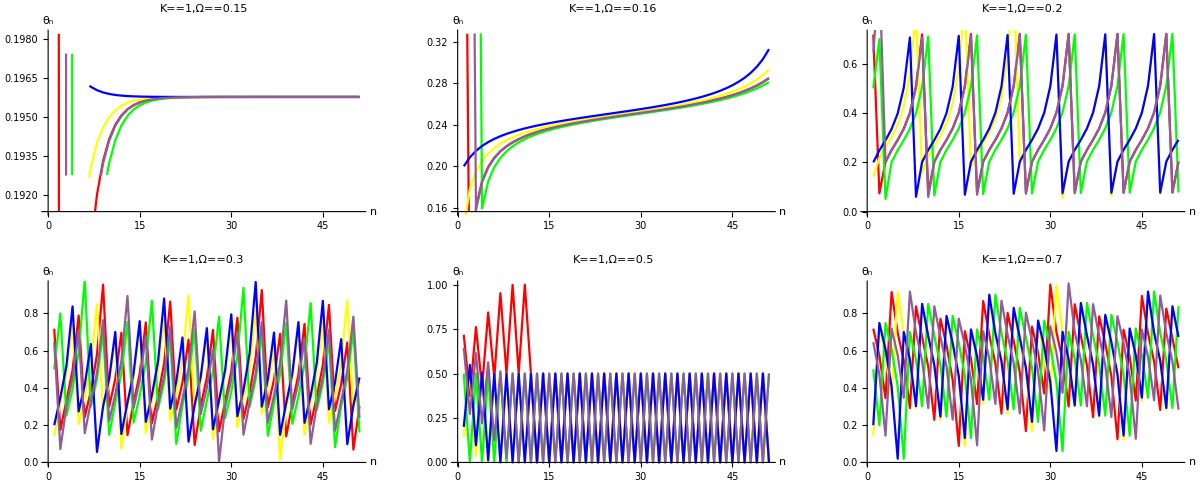

```mathematica
Show[GraphicsGrid[
Partition[Function[p,i=1;Block[{$DisplayFunction=Identity},
Show[
ListLinePlot[CircleMap[p,50,#//N],AxesLabel->TraditionalForm/@{n,Subscript[θ, n]},PlotStyle->color[[i++]],PlotLabel->TraditionalForm[label@@p]]&/@FractionalPart[{E,Pi,2.5,.2,Sqrt[7]}]
]]]/@{{1,.15},{1,.16},{1,.2},{1,.3},{1,.5},{1,.7}},
3,3,{1,1},{}]
]
]
```